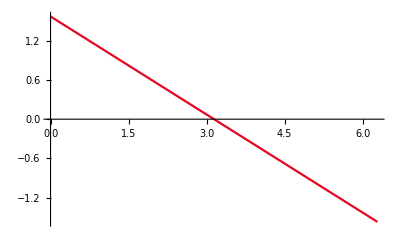

```mathematica
(*原函数图像*)
f[x_]:=(Pi-x)/2;
img1=Plot[(Pi-x)/2,{x,0,2 Pi},PlotStyle->ColorData[3,"ColorList"]]
```

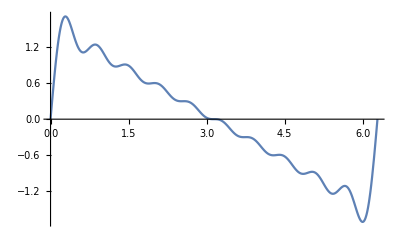
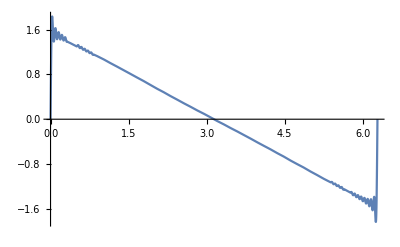
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*N=10,100,无变形逼近对比图结果*)
fn[x_,n_]:=Sum[Sin[w x]/w,{w,1,n}];
img2=Plot[fn[x,10],{x,0,2 Pi}];
img3=Plot[fn[x,100],{x,0,2 Pi}];
{img1,img2,img3}
```

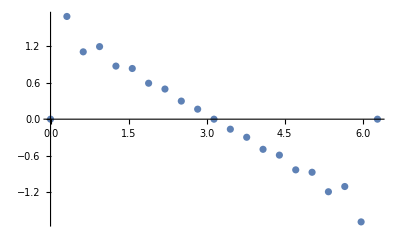
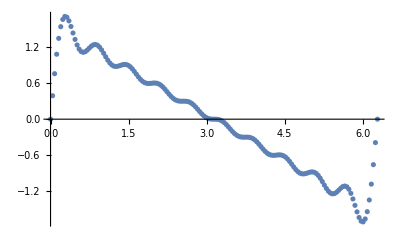
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*N=10,m=20，160时，无变形逼近结果*)
m=20;
deltax=2 Pi/m;
table11=Table[{i deltax,fn[i deltax,10]},{i,0,m}];
img21=ListPlot[table11];
m=160;
deltax=2 Pi/m;
table12=Table[{i deltax,fn[i deltax,10]},{i,0,m}];
img22=ListPlot[table12];
{img1,img21,img22}
```

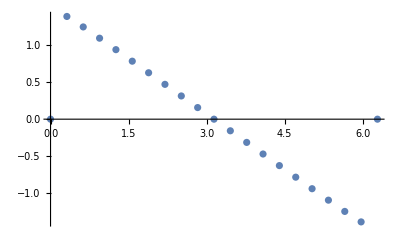
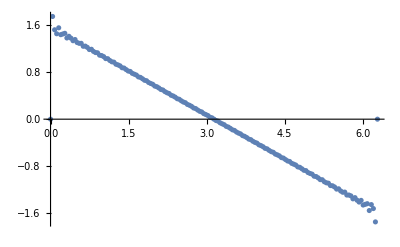
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*N=100,m=20，160时，无变形逼近结果*)
m=20;
deltax=2 Pi/m;
table21=Table[{i deltax,fn[i deltax,100]},{i,0,m}];
img31=ListPlot[table21];
m=160;
deltax=2 Pi/m;
table22=Table[{i deltax,fn[i deltax,100]},{i,0,m}];
img32=ListPlot[table22];
{img1,img31,img32}
```

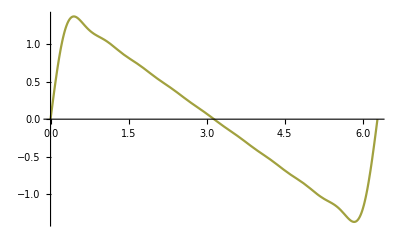
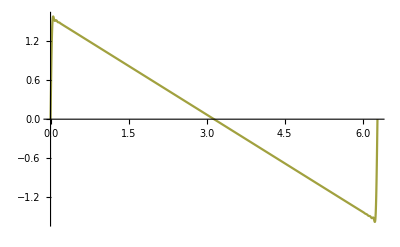
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*N=10,100,变形函数的逼近对比图结果*)
fn2[x_,n_]:=Sum[Sin[w Pi/n]/(w Pi/n) Sin[w x]/w,{w,1,n}];
img4=Plot[fn2[x,10],{x,0,2 Pi},PlotStyle->ColorData[5,"ColorList"]];
img5=Plot[fn2[x,100],{x,0,2 Pi},PlotStyle->ColorData[5,"ColorList"]];
{img1,img4,img5}
```

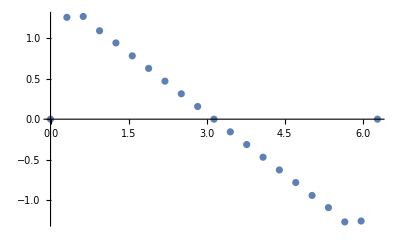
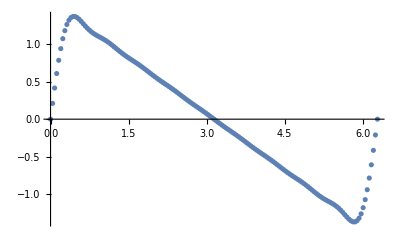
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*N=10,m=20，160时，变形逼近结果*)
m=20;
deltax=2 Pi/m;
table31=Table[{i deltax,fn2[i deltax,10]},{i,0,m}];
img41=ListPlot[table31];
m=160;
deltax=2 Pi/m;
table32=Table[{i deltax,fn2[i deltax,10]},{i,0,m}];
img42=ListPlot[table32];
{img1,img41,img42}
```

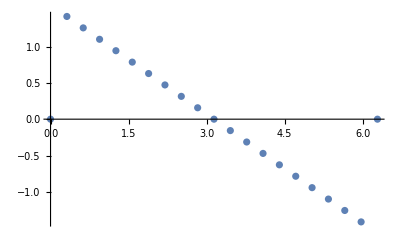
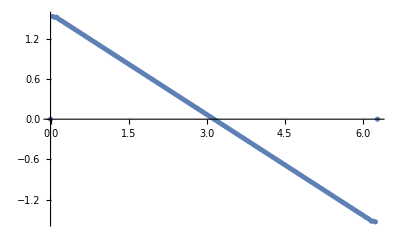
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*N=100,m=20，160时，变形逼近结果*)
m=20;
deltax=2 Pi/m;
table41=Table[{i deltax,fn2[i deltax,100]},{i,0,m}];
img51=ListPlot[table41];
m=160;
deltax=2 Pi/m;
table42=Table[{i deltax,fn2[i deltax,100]},{i,0,m}];
img52=ListPlot[table42];
{img1,img51,img52}
```

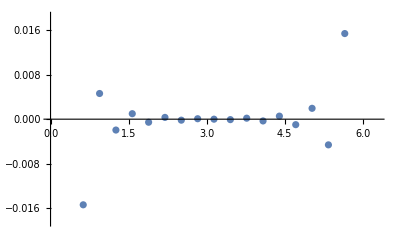
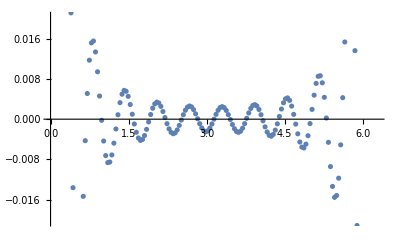

```mathematica
(*N=10,M=20,160,差值*)
m=20;
deltax=2 Pi/m;
table51=Table[{i deltax,f[i deltax]-fn2[i deltax,10]},{i,0,m}];
img61=ListPlot[table51];
m=160;
deltax=2 Pi/m;
table52=Table[{i deltax,f[i deltax]-fn2[i deltax,10]},{i,0,m}];
img62=ListPlot[table52];
{img61,img62}
```

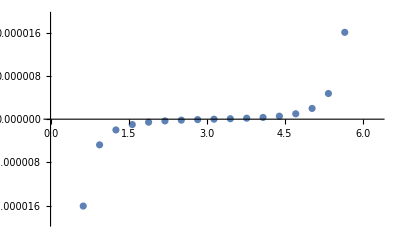
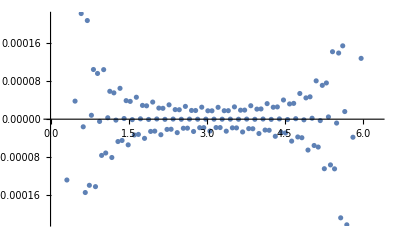

```mathematica
(*N=100,M=20,160,差值*)
m=20;
deltax=2 Pi/m;
table61=Table[{i deltax,f[i deltax]-fn2[i deltax,100]},{i,0,m}];
img71=ListPlot[table61];
m=160;
deltax=2 Pi/m;
table62=Table[{i deltax,f[i deltax]-fn2[i deltax,100]},{i,0,m}];
img72=ListPlot[table62];
{img71,img72}
```